# Practice 4 -- Extinction spectra of elliptical and spherical metallic particles

## 1. Comparison of extinction cross-section bands of elliptical and spherical nanoparticles.

```mathematica
(*universal constants*)
cL=3*10^8;
ϵinf=1^2;

(*fix the Drude material properties*)
ωp=8.7*10^15;
γ=1*10^15;
λp=(2*π*cL)/ωp;
λγ=(2*π*cL)/γ;

(*fix surrounding media properties*)
ϵD=1;

(*particles spatial parameters*)
aSph=20*10^-9;
a=30*10^-9;
b=20*10^-9;
c=10*10^-9;
La=2/11; 
Lb=3/11; 
Lc=6/11;

(*dielectric permittivity*)
ϵ[λ_]:=ϵinf-1/(λp^2*(1/λ^2-1/λγ^2))+ⅈ*λ/(λγ*λp^2*(1/λ^2+1/λγ^2));

(*polariability of a spherical particle*)
α[λ_]:=aSph^3*(ϵ[λ]-ϵD)/(ϵ[λ]+2*ϵD);

(*extinction cross-section of a spherical particle*)
σextSph[λ_]:=(8*π^2*√ϵD)/λ*Im[α[λ]];
(*polarizabilities along each axis for an elliptical particle*)
αa[λ_]:=a*b*c*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*La));
αb[λ_]:=a*b*c*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*Lb));
αc[λ_]:=a*b*c*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*Lc));
(*extinction cross-section of an elliptical particle*)
σexta[λ_]:=(8*π^2*√ϵD)/λ*Im[αa[λ]];
σextb[λ_]:=(8*π^2*√ϵD)/λ*Im[αb[λ]];
σextc[λ_]:=(8*π^2*√ϵD)/λ*Im[αc[λ]];
```

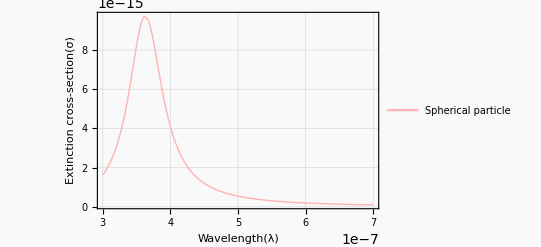

```mathematica
Plot[σextSph[λ],{λ,300*10^-9,0.7*10^-6},
PlotRange->All,
Frame->True,
FrameLabel->{"Wavelength(λ)","Extinction cross-section(σ)"},
FrameStyle->Directive[Black,Medium],
PlotStyle->{{Thick,Lighter[Pink,0.4]}},
PlotTheme->"Scientific",
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
Background->Lighter[Gray,0.95],
PlotLegends->Placed[{"Spherical particle"},{0.74,0.7}]]
```

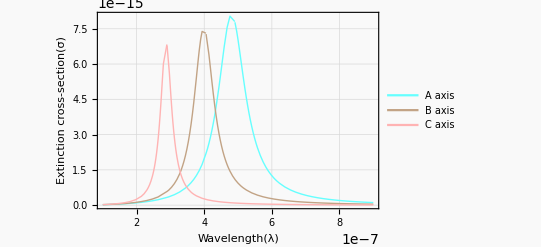

```mathematica
Plot[{σexta[λ],σextb[λ],σextc[λ]},{λ,100*10^-9,0.9*10^-6},
PlotRange->All,
Frame->True,
FrameLabel->{"Wavelength(λ)","Extinction cross-section(σ)"},
FrameStyle->Directive[Black,Medium],
PlotStyle->{{Thick,Lighter[Cyan,0.4]},{Thick,Lighter[Brown,0.4]},{Thick,Lighter[Pink,0.4]}},
PlotTheme->"Scientific",
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
Background->Lighter[Gray,0.95],
PlotLegends->Placed[{"A axis","B axis","C axis"},{0.74,0.77}]]
```

## 2. Spherical nanoparticle vs. oblate/prolate spheroid

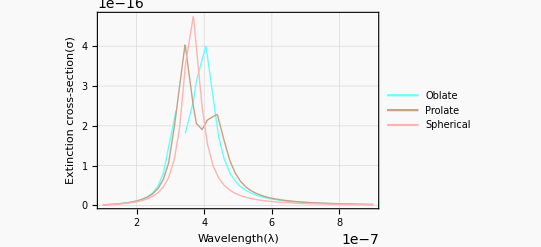

```mathematica
(*particle parameters*)
V=6*10^-24;
exc=.8;
(*depolarisation factors*)
LaPr=1/(1+2/((1-exc^2)^(1/2)));
LbPr=1/(2+(1-exc^2)^(1/2)); (*prolate (cigar)*)
LaOb=1/(2+1/((1-exc^2)^(1/2)));
LbOb=1/(1+2*(1-exc^2)^(1/2)); (*oblate (disk)*)
(*Polarizability*)
αaPr[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LaPr));
αbPr[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LbPr));
αPr[λ_]:=(αaPr[λ]+2αbPr[λ])/3;
αaOb[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LaOb));
αbOb[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LbOb));
αOb[λ_]:=(2αaOb[λ]+αbOb[λ])/3;

(*extinction cross section*)
σextPr[λ_]:=(8*π^2*√ϵD)/λ*Im[αPr[λ]];
σextOb[λ_]:=(8*π^2*√ϵD)/λ*Im[αOb[λ]];
Plot[{σextOb[λ],σextPr[λ],σextSph[λ]/20},{λ,100*10^-9,0.9*10^-6},
PlotRange->All,
Frame->True,
FrameLabel->{"Wavelength(λ)","Extinction cross-section(σ)"},
FrameStyle->Directive[Black,Medium],
PlotStyle->{{Thick,Lighter[Cyan,0.4]},{Thick,Lighter[Brown,0.4]},{Thick,Lighter[Pink,0.4]}},
PlotTheme->"Scientific",
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
Background->Lighter[Gray,0.95],
PlotLegends->Placed[{"Oblate","Prolate","Spherical"},{0.74,0.77}]]
```

## 3. Extinction dependance on eccentricity

```mathematica
Manipulate[(*Depolarization factors for oblate and prolate*)LaPr=1/(1+2/(1-exc^2)^(1/2));
LbPr=1/(2+(1-exc^2)^(1/2));
LaOb=1/(2+1/(1-exc^2)^(1/2));
LbOb=1/(1+2*(1-exc^2)^(1/2));
(*Polarizabilities for prolate (cigar) nanoparticles*)αaPr[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LaPr));
αbPr[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LbPr));
αPr[λ_]:=(αaPr[λ]+2 αbPr[λ])/3;
σextPr[λ_]:=(8*π^2*Sqrt[ϵD])/λ*Im[αPr[λ]];
(*Polarizabilities for oblate (disk) nanoparticles*)αaOb[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LaOb));
αbOb[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*LbOb));
αOb[λ_]:=(2 αaOb[λ]+αbOb[λ])/3;
σextOb[λ_]:=(8*π^2*Sqrt[ϵD])/λ*Im[αOb[λ]];
(*Plotting the extinction cross-section spectra*)Plot[{σextOb[λ],σextPr[λ]},{λ,100*10^-9,900*10^-9},PlotRange->All,Frame->True,FrameLabel->{"Wavelength (λ)","Extinction cross-section (σ)"},FrameStyle->Directive[Black,Medium],PlotStyle->{{Thick,Lighter[Cyan,0.4]},{Thick,Lighter[Brown,0.4]}},PlotTheme->"Scientific",GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Background->Lighter[Gray,0.95],PlotLegends->Placed[{"Oblate","Prolate"},{0.75,0.8}],
Epilog->{Text[Style["ecc = "<> ToString[exc],18,Black,FontFamily->"Times New Roman"],{2.3*10^-7,2*10^-16}]}],{{exc,0.5},0.1,0.99,0.01,Appearance->"Labeled"}]
```

RuleDelayed::rhs: Pattern λ_ appears on the right-hand side of rule Polarizability[exc_,λ_]:>Module[{La,Lb,α},{La,Lb}=AveragedDepolarizationFactors[exc];α[λ_]:=(V Power[«2»]) (Plus[«2»] Power[«2»])+2 (V Power[«2»]) (Plus[«2»] Power[«2»]);Im[α[λ]]].

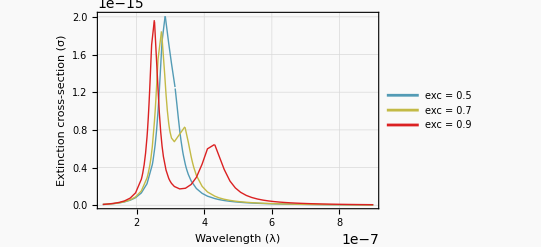

```mathematica
(*Параметры частицы и среды*)
V=6*10^-24;(*объем частицы*)
ϵD=1.33^2;(*диэлектрическая проницаемость среды*)

(*Деполяризационные факторы*)
DepolarizationFactors[exc_,theta_]:=Module[{La,Lb},La=1/(1+2/(1-exc^2)^(1/2));(*продольный фактор*)Lb=1/(2+(1-exc^2)^(1/2));(*поперечный фактор*){La,Lb}];

(*Усредненные деполяризационные факторы для случайного ансамбля*)
AveragedDepolarizationFactors[exc_]:=Module[{La,Lb,weight},weight[θ_]:=Sin[θ];(*вес ориентации (равномерное распределение)*)La=NIntegrate[weight[θ]*(1/(1+2/(1-exc^2)^(1/2))),{θ,0,π}];
Lb=NIntegrate[weight[θ]*(1/(2+(1-exc^2)^(1/2))),{θ,0,π}];
{La,Lb}];

(*Поляризуемость для ансамбля*)
Polarizability[exc_,λ_]:=Module[{La,Lb,α},{La,Lb}=AveragedDepolarizationFactors[exc];
α[λ_]:=V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*La))+2*V/(4*π)*(ϵ[λ]/ϵD-1)/(3*(1+(ϵ[λ]/ϵD-1)*Lb));
Im[α[λ]]];

(*Сечение экстинкции*)
ExtinctionCrossSection[exc_,λ_]:=(8*π^2*Sqrt[ϵD])/λ*Polarizability[exc,λ];

(*Построение графиков для разных эксцентриситетов*)
excValues={0.5,0.7,0.9};
Plot[Evaluate[Table[ExtinctionCrossSection[exc,λ],{exc,excValues}]],{λ,100*10^-9,900*10^-9},
PlotRange->All,
Frame->True,
FrameLabel->{"Wavelength (λ)","Extinction cross-section (σ)"},
FrameStyle->Directive[Black,Medium],
PlotStyle->Table[{Thick,ColorData["Rainbow"][i/Length[excValues]]},
{i,Length[excValues]}],
PlotLegends->Placed[Table["exc = "<>ToString[exc],{exc,excValues}],{0.6,0.6}],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
Background->Lighter[Gray,0.95]]
```